```mathematica
Clear["Global`*"]
States={0.6,0.4};
TransitionMatrix={{0.7,0.3},{0.4,0.6}};
EmissionMatrix={{0.5,0.4,0.1},{0.1,0.3,0.6}};
dmm=DiscreteMarkovProcess[States,TransitionMatrix];
hmm=HiddenMarkovProcess[States,TransitionMatrix,EmissionMatrix];
```

## Существует три основных задачи, которые могут быть решены при использовании скрытых марковских моделях.

### Задача 1.Найти вероятность того, что данная наблюдаемая последовательность построена именно для данной модели.

К сути этой задачи можно подойти и с другой стороны: насколько выбранная СММ соответствует заданной наблюдаемой последовательности. Такой подход имеет большую практическую ценность. Например, если у нас стоит вопрос выбора наилучшей модели из набора уже существующих, то решение первой задачи дает нам ответ на этот вопрос.

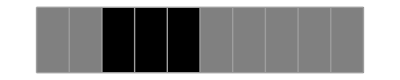

{1,1,2,2,2,1,1,1,1,1}

{1,1,3,3,3,2,1,2,2,1}

```mathematica
data=RandomFunction[hmm,{1,10},Method->{Automatic,"IncludeHiddenStates"->True}];
states=data["HiddenStates"];
ArrayPlot[{states["Values"]},Mesh->All]
data["HiddenStates"]["Values"]
data["Values"]
```

```mathematica
jointLikelihood[states_,emissions_]:=Likelihood[DiscreteMarkovProcess[hmm],states]*Times@@MapThread[Part[EmissionMatrix,#1,#2]&,{states,emissions}]

jointLikelihood[states["Values"],data["Values"]]
Log[%]
```

3.76391×10^-6

-12.4901

```mathematica
jointLogLikelihood[states_,emissions_]:=LogLikelihood[DiscreteMarkovProcess[hmm],states]+Total[MapThread[Log[Part[EmissionMatrix,#1,#2]]&,{states,emissions}]]

jointLogLikelihood[{1,1,2,2,2,2,1,1,1,1},data["Values"]]
Exp[%]
```

-12.9319

2.41965×10^-6

### Задача 2.Необходимо подобрать последовательность состояний системы, которая лучше всего соответствует наблюдаемой последовательности, то есть «объясняет» наблюдаемую последовательность.

в которой мы пытаемся понять, что же происходит в скрытой части модели, то есть найти «правильную» последовательность, которую проходит модель. Совершенно ясно, что абсолютно точно нельзя определить эту последовательность.

```mathematica
emis={1,2,3,1,2,3}
FindHiddenMarkovStates[emis,hmm]
```

{1,2,3,1,2,3}

{1,1,2,1,1,2}

### Задача 3.Найти вероятность того, что данная наблюдаемая последовательность построена именно для данной модели.

состоит в оптимизации модели таким образом, чтобы она как можно лучше описывала реальную наблюдаемую последовательность. Наблюдаемая последовательность, по которой оптимизируется СММ, принято называть обучающей последовательностью, поскольку с помощью нее мы «обучаем» модель. Задача обучения СММ — это важнейшая задача для большинства проектируемых СММ, поскольку она заключается в оптимизации параметров СММ на основе обучающей наблюдаемой последовательности, то есть создается модель, наилучшим образом описывающая реальные процессы.

## Задача 3. (пример из MathLab)

```mathematica
Clear["Global*`"]
Trans={{0.9,0.1},{0.05,0.95}};
Emis={{1/6,1/6,1/6,1/6,1/6,1/6},{7/12,1/12,1/12,1/12,1/12,1/12}};
hmm=HiddenMarkovProcess[ {1,0},Trans,Emis]
```

HiddenMarkovProcess[{1,0},{{0.9,0.1},{0.05,0.95}},{{1/6,1/6,1/6,1/6,1/6,1/6},{7/12,1/12,1/12,1/12,1/12,1/12}}]

Для проверки точности, вычислим процент реальных состояний последовательности, которая согласуется с likelystates последовательности (Алгоритм Витерби)

```mathematica
k=1000;
data=RandomFunction[hmm,{1,k},Method->{Automatic,"IncludeHiddenStates"->True}];
states=data["HiddenStates"]["Values"];
seq=data["Values"];
likelystates=FindHiddenMarkovStates[seq,hmm];
Count[Transpose[{states,likelystates}],{x_,x_}]/k //N
```

0.835

Для проверки точности, вычислим процент реальных состояний последовательности, которая согласуется с likelystates последовательности (Алгоритм Апостериорная вероятность)

```mathematica
k=1000;
data=RandomFunction[hmm,{1,k},Method->{Automatic,"IncludeHiddenStates"->True}];
states=data["HiddenStates"]["Values"];
seq=data["Values"];
likelystates=FindHiddenMarkovStates[seq,hmm,"PosteriorDecoding"];
Count[Transpose[{states,likelystates}],{x_,x_}]/k //N
```

0.84

Поиск параметров процесса по состояниям и наблюдениям (SupervisedTraining)

```mathematica
espss=EstimatedProcess[seq,HiddenMarkovProcess[2,6],ProcessEstimator->{"SupervisedTraining","StateData"->states}];
{{espss[[1]],hmm[[1]]}}//MatrixForm
{{espss[[2]],hmm[[2]]}}//MatrixForm
{{espss[[3]],hmm[[3]]//N}}//MatrixForm
```

((1.
0.) | (1
0))

((0.885017 | 0.114983
0.0449438 | 0.955056) | (0.9 | 0.1
0.05 | 0.95))

((0.12892 | 0.212544 | 0.174216 | 0.188153 | 0.142857 | 0.15331
0.57223 | 0.0771388 | 0.0659187 | 0.0771388 | 0.0995792 | 0.107994) | (0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667
0.583333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333))

Поиск параметров процесса по данным и известным параметром процесса (автомат)

```mathematica
esp=EstimatedProcess[seq,HiddenMarkovProcess[2,6],hmm]
{{esp[[1]],hmm[[1]]}}//MatrixForm
{{esp[[2]],hmm[[2]]}}//MatrixForm
{{esp[[3]],hmm[[3]]//N}}//MatrixForm
```

HiddenMarkovProcess[{1.,0.},{{0.920466,0.0795339},{0.0353286,0.964671}},{{0.170286,0.197367,0.179029,0.165788,0.154796,0.132734},{0.571647,0.0784887,0.0591837,0.0828202,0.0922705,0.11559}}]

((1.
0.) | (1
0))

((0.920466 | 0.0795339
0.0353286 | 0.964671) | (0.9 | 0.1
0.05 | 0.95))

((0.170286 | 0.197367 | 0.179029 | 0.165788 | 0.154796 | 0.132734
0.571647 | 0.0784887 | 0.0591837 | 0.0828202 | 0.0922705 | 0.11559) | (0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667
0.583333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333))

Поиск параметров процесса по данным и известным параметром процесса (BaumWelch) максимальное правдоподобие  мат. ожидания

```mathematica
espbw=EstimatedProcess[seq,HiddenMarkovProcess[2,6],hmm,ProcessEstimator->"BaumWelch"];
{{espbw[[1]],hmm[[1]]}}//MatrixForm
{{espbw[[2]],hmm[[2]]}}//MatrixForm
{{espbw[[3]],hmm[[3]]//N}}//MatrixForm
```

((1.
0.) | (1
0))

((0.920466 | 0.0795339
0.0353286 | 0.964671) | (0.9 | 0.1
0.05 | 0.95))

((0.170286 | 0.197367 | 0.179029 | 0.165788 | 0.154796 | 0.132734
0.571647 | 0.0784887 | 0.0591837 | 0.0828202 | 0.0922705 | 0.11559) | (0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667
0.583333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333))

Поиск параметров процесса по данным и известным параметром процесса (ViterbiTraining) нахождение наиболее вероятной последовательности с контролируемым обучением

```mathematica
espv=EstimatedProcess[seq,HiddenMarkovProcess[2,6],hmm,ProcessEstimator->"ViterbiTraining"];
{{espv[[1]],hmm[[1]]}}//MatrixForm
{{espv[[2]],hmm[[2]]}}//MatrixForm
{{espv[[3]],hmm[[3]]//N}}//MatrixForm
```

((1.
0.) | (1
0))

((0.971631 | 0.0283688
0.0097629 | 0.990237) | (0.9 | 0.1
0.05 | 0.95))

((0.173759 | 0.202128 | 0.180851 | 0.159574 | 0.156028 | 0.12766
0.551532 | 0.0821727 | 0.0640669 | 0.0891365 | 0.0947075 | 0.118384) | (0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667
0.583333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333))

Поиск параметров процесса по данным и известным параметром процесса (StateClustering) использовать кластеризацию с последующим пс контролируемым обучением

```mathematica
espc=EstimatedProcess[seq,HiddenMarkovProcess[2,6],hmm,ProcessEstimator->"StateClustering"];
{{espc[[1]],hmm[[1]]}}//MatrixForm
{{espc[[2]],hmm[[2]]}}//MatrixForm
{{espc[[3]],hmm[[3]]//N}}//MatrixForm
```

((1.
0.) | (1
0))

((0.356725 | 0.643275
0.333333 | 0.666667) | (0.9 | 0.1
0.05 | 0.95))

((0. | 0. | 0. | 0.318713 | 0.327485 | 0.353801
0.676292 | 0.176292 | 0.147416 | 0. | 0. | 0.) | (0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667
0.583333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333 | 0.0833333))

Поиск параметров процесса по данным и частично известным параметром процесса с последовательным приближением.
 Внимание!!! работать будет только для BaumWelch, остальные с контролируемым обучением (ViterbiTraining , StateClustering)

```mathematica
espi=EstimatedProcess[seq,HiddenMarkovProcess[2,6],hmm,ProcessEstimator->"BaumWelch"];
Do[
espi=EstimatedProcess[seq,HiddenMarkovProcess[2,6],espi,ProcessEstimator->"BaumWelch"],
{i,1,100}]
{{espi[[1]],espbw[[1]]}}//MatrixForm
{{espi[[2]],espbw[[2]]}}//MatrixForm
{{espi[[3]],espbw[[3]]//N}}//MatrixForm
```

((1.
0.) | (1.
0.))

((0.921393 | 0.0786067
0.034805 | 0.965195) | (0.920466 | 0.0795339
0.0353286 | 0.964671))

((0.170615 | 0.1973 | 0.178946 | 0.165796 | 0.154768 | 0.132576
0.571161 | 0.0786188 | 0.0593215 | 0.0828855 | 0.0923353 | 0.115678) | (0.170286 | 0.197367 | 0.179029 | 0.165788 | 0.154796 | 0.132734
0.571647 | 0.0784887 | 0.0591837 | 0.0828202 | 0.0922705 | 0.11559))

Поиск параметров процесса по данным и частично известным параметром процесса

```mathematica
EstimatedProcess[seq,HiddenMarkovProcess[
{1,0},
{{p,1-p},{1-q,q}},
{{1/6,1/6,1/6,1/6,1/6,1/6},{7/12,1/12,1/12,1/12,1/12,1/12}}
],
{{p,0.8},{q,0.9}}]
```

HiddenMarkovProcess[{1.,0.},{{0.920517,0.0794831},{0.0352995,0.9647}},{{0.170303,0.197364,0.179024,0.165788,0.154794,0.132726},{0.571619,0.078496,0.0591914,0.0828239,0.0922742,0.115595}}]

Поиск параметров процесса по данным и неизвестным параметра процесса

```mathematica
EstimatedProcess[seq,HiddenMarkovProcess[2,6]]
EstimatedProcess[seq,HiddenMarkovProcess[2,6],ProcessEstimator->"ViterbiTraining"]
```

HiddenMarkovProcess[{3.43579×10^-18,1.},{{0.500509,0.499491},{0.701875,0.298125}},{{0.454902,0.107741,0.124584,0.0858437,0.123732,0.103197},{0.431114,0.127582,0.0583169,0.141473,0.0955483,0.145966}}]

HiddenMarkovProcess[{0.,1.},{{0.,1.},{1.,0.}},{{0.438,0.118,0.112,0.108,0.108,0.116},{0.452,0.114,0.082,0.11,0.116,0.126}}]

Поиск параметров процесса по данным неизвестным параметром процесса, но разным количеством исходных данных

```mathematica
k=1000;
data1=RandomFunction[hmm,{1,k},1];
EstimatedProcess[data1,HiddenMarkovProcess[2,6]]

data100=RandomFunction[hmm,{1,k},100];
EstimatedProcess[data100,HiddenMarkovProcess[2,6]]
```

HiddenMarkovProcess[{0.469448,0.530552},{{0.496675,0.503325},{0.69212,0.30788}},{{0.454208,0.101628,0.105215,0.10994,0.101393,0.127616},{0.453714,0.102512,0.104705,0.112457,0.100459,0.126153}}]

HiddenMarkovProcess[{0.465712,0.534288},{{0.496627,0.503373},{0.692082,0.307918}},{{0.445852,0.11215,0.109133,0.110741,0.110525,0.111599},{0.444517,0.113219,0.108722,0.113422,0.109777,0.110343}}]

```mathematica
datan=RandomFunction[hmm,{1,k}];
seqn=data["Values"];
TRANSGUESS={{.85,.15},{.1,.9}};
EMISGUESS={{.17,.16,.17,.16,.17,.17},{.6,.08,.08,.08,.08,.08}};
EstimatedProcess[seqn,HiddenMarkovProcess[2,6],HiddenMarkovProcess[{1,0},TRANSGUESS,EMISGUESS],ProcessEstimator->"BaumWelch"]
EstimatedProcess[seqn,HiddenMarkovProcess[2,6],HiddenMarkovProcess[{1,0},TRANSGUESS,EMISGUESS],ProcessEstimator->"ViterbiTraining"]
EstimatedProcess[seqn,HiddenMarkovProcess[2,6],HiddenMarkovProcess[{1,0},TRANSGUESS,EMISGUESS],ProcessEstimator->"StateClustering"]
```

HiddenMarkovProcess[{1.,0.},{{0.920526,0.0794739},{0.0352964,0.964704}},{{0.170313,0.197361,0.179022,0.165787,0.154794,0.132724},{0.571619,0.078496,0.0591916,0.0828238,0.0922739,0.115596}}]

HiddenMarkovProcess[{1.,0.},{{0.971631,0.0283688},{0.0097629,0.990237}},{{0.173759,0.202128,0.180851,0.159574,0.156028,0.12766},{0.551532,0.0821727,0.0640669,0.0891365,0.0947075,0.118384}}]

HiddenMarkovProcess[{1.,0.},{{0.356725,0.643275},{0.333333,0.666667}},{{0.,0.,0.,0.318713,0.327485,0.353801},{0.676292,0.176292,0.147416,0.,0.,0.}}]